# GetTissueInsidePolygon Example

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51c (08 June 2017)) loaded Fri 9 Jun 2017 17:15:48
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

### Define a tissue and a collection of points that define the vertices of a polygon

```mathematica
T=TemplateRandomSquareGrid[100, {-10,-10}, {10,10}];
```

```mathematica
points=Table[{7.*Cos[x], 10.*Sin[x]}, {x,0,(11/6)*Pi, Pi/6}]
```

{{7.,0.},{6.06218,5.},{3.5,8.66025},{0.,10.},{-3.5,8.66025},{-6.06218,5.},{-7.,0.},{-6.06218,-5.},{-3.5,-8.66025},{0.,-10.},{3.5,-8.66025},{6.06218,-5.}}

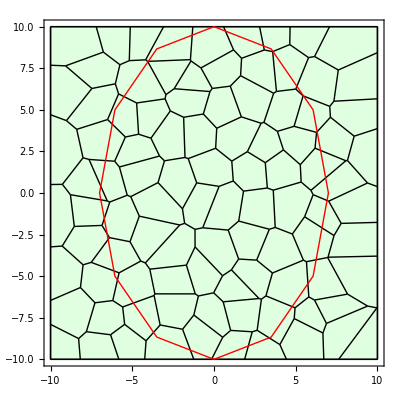

```mathematica
ShowTissue[T, Frame-> True, Epilog-> {Red,Thick,  Line[Append[points, points[[1]]]]}]
```

### Extract a tissue that contains the points whose center is INSIDE the polygon

```mathematica
Q=GetTissueInsidePolygon[T, points];
```

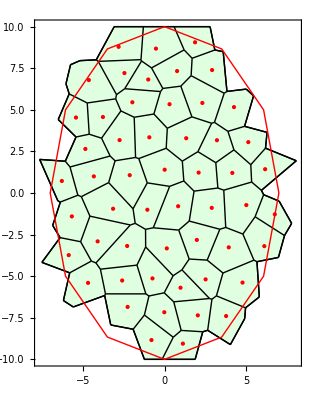

```mathematica
ShowTissue[Q, Frame-> True, Epilog-> {Red,Thick, Point[Centeroid[Q]],  Line[Append[points, points[[1]]]]}]
```